## Linguistics

Manuel Aguilar

I did this notebook at the request of a friend. My friend studies linguistics in the University of Texas at El Paso. However, studying linguistics does not stop him form having interest in computational sciences. The purpose of this notebook is to highlight the Wolfram Language’s capability of manipulating text and performing computations. All computations performed in this notebook are part of the core language.

https://www.wolfram.com/language/11/text-and-language-processing/

## Alphabets

```mathematica
Alphabet["Greek"]
```

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}

```mathematica
Alphabet["Hebrew"]
```

{א,ב,ג,ד,ה,ו,ז,ח,ט,י,כ,ל,מ,נ,ס,ע,פ,צ,ק,ר,ש,ת}

```mathematica
Alphabet["Arabic"]
```

{ا,ب,ت,ث,ج,ح,خ,د,ذ,ر,ز,س,ش,ص,ض,ط,ظ,ع,غ,ف,ق,ك,ل,م,ن,ه,و,ي}

```mathematica
Alphabet["Spanish"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,r,s,t,u,v,w,x,y,z}

## Set Directory With Sample Data

Print current working directory

```mathematica
NotebookDirectory[]
```

/home/user/Desktop/projects/open/notebooks_dev/final/

Change Current Directory to specified path.

```mathematica
SetDirectory[NotebookDirectory[]<>"/data"]
```

/home/user/Desktop/projects/open/notebooks_dev/final/data

Use external files by importing them

```mathematica
?Import
```

## Import Properties

Mathematica import support a series of elements that can specified when import files. In this case a WAV file.

```mathematica
Import["you-can-do-it.wav",{"WAV","Elements"}]//TableForm
```

Audio
AudioChannels
AudioEncoding
AudioFile
Data
Duration
Length
MetaInformation
RawMetaInformation
SampleDepth
SampledSoundList
SampleRate
Sound

#### Look at all the properties

```mathematica
Manipulate[Import["you-can-do-it.wav",e],{{e,"Audio","Options"},Import["you-can-do-it.wav",{"WAV","Elements"}]}]
```

#### Import for our Notebooks

```mathematica
fullWavFile1 = Import["you-can-do-it.wav",{"WAV","Sound"}];
```

```mathematica
fullWavFile2 = Import["youre-so-cute.wav",{"WAV","Sound"}];
```

```mathematica
fullWavFile3 = Import["you-silly-thing.wav",{"WAV","Sound"}];
```

```mathematica
wavFile1  = Import["you-can-do-it.wav",{"WAV"}];
```

```mathematica
wavFile2 = Import["youre-so-cute.wav",{"WAV"}];
```

```mathematica
wavFile3 = Import["you-silly-thing.wav",{"WAV"}];
```

#### Analysis of Sound

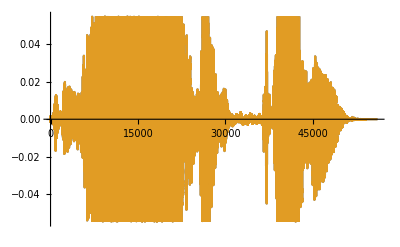

```mathematica
Import["you-silly-thing.wav",{"WAV","Data"}]//ListLinePlot
```

#### Time Series Object

```mathematica
ts = AudioLocalMeasurements[wavFile1,"RMSAmplitude"]
```

TimeSeries[…]

```mathematica
AudioMeasurements[wavFile1,{"MinMax","Mean","StandardDeviation","RMSAmplitude","ZeroCrossings"},"Dataset"]
```

Dataset[<>]

```mathematica
Manipulate[ts[e],{e,ts["Properties"]}]
```

#### Overlay Plots and Combine Plots

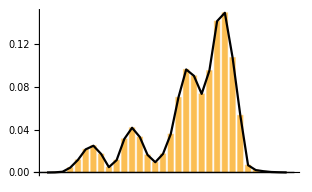

```mathematica
Show[BarChart[ts["Values"]],ListLinePlot[ts["Values"],PlotStyle->Black]]
```

```mathematica
Manipulate[GraphicsColumn[{
Show[AudioPlot[wav],ListLinePlot[ts,PlotStyle->Pink]],
Spectrogram[wav],
AudioMeasurements[wav,{"MinMax","Mean","StandardDeviation","RMSAmplitude","ZeroCrossings"},"Dataset"],
AudioMeasurements[wav,{"SpectralCentroid","SpectralFlatness","SpectralRollOff","SpectralSpread"},"Dataset"]
},ImageSize->Large],{{wav,wavFile1,"Wav Files"},{wavFile1,wavFile2,wavFile3}}]
```

## Wolfram Data Repository

https://datarepository.wolframcloud.com/

I decided to get a dataset that has text as its principle feature.

```mathematica
ResourceObject["Presidential Nomination Acceptance Speeches"]
```

ResourceObject[…]

Take these speeches for example. They are of the President of the United States from 1864 to 2012.

```mathematica
df = ResourceData["Presidential Nomination Acceptance Speeches"];
```

```mathematica
df[1,All]
```

Dataset[<>]

```mathematica
df[1;;10,{"Person","Text"}]
```

Dataset[<>]

```mathematica
Manipulate[
GraphicsRow[{
df[e,"Person"],WordCloud[DeleteStopwords[df[e,"Text"]]]
}],{{e,1,"Speech"},1,Length[df],1},ContinuousAction->False]
```

### Movie Review

Using the same wolfram data repository we are able to get movie reviews and perform sentiment analysis.

```mathematica
ResourceObject["Sample Data: Movie Review Sentence Polarity"]
```

ResourceObject[…]

#### Training Data

```mathematica
movies = RandomSample[ResourceData["Sample Data: Movie Review Sentence Polarity"],1000];
```

```mathematica
prepData = #["Review"]->#["Sentiment"]&/@Normal[movies];
```

```mathematica
c = Classify[prepData]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Text
Classes | ,,negativepositive
Accuracy | (61.5.) %
Method | Markov
Single evaluation time | 2.94 ms/example
Batch evaluation speed | 23.4 examples/ms
Loss | 1.48 ± 0.25
Model memory | 337. kB
Training examples used | 1000 examples
Training time | 1.04 s
 |

#### Test Data

```mathematica
testData = ResourceData["Sample Data: Movie Review Sentence Polarity","TestData"];
```

Choose whatever numbers you want to index in the test data.

```mathematica
t1 = testData⟦3⟧
```

offers that rare combination of entertainment and education . →positive

```mathematica
t2 = testData⟦83⟧
```

it's a terrific american sports movie and dennis quaid is its athletic heart . →positive

```mathematica
t3 = testData⟦431⟧
```

the most compelling wiseman epic of recent years . →positive

Test your model here.

```mathematica
c[First[t1]]
```

positive

```mathematica
c[First[t2]]
```

positive

```mathematica
c[First[t3]]
```

positive

Measure your model’s performance.

```mathematica
cm = ClassifierMeasurements[c,testData];
```

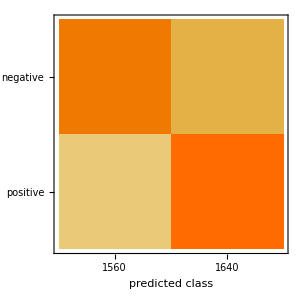

```mathematica
cm["ConfusionMatrixPlot"]
```